```mathematica
(* Example Mathematica notebook code for Figure 4 in main text and Figures S5, S10, and S11 in the Supplementary Information *)
(* Run using Mathematica version 12.0.0.0 on Mac OS X x86 (64-bit) *)
```

```mathematica
(* define parameters *)

(* Npatches patches, Moran process, size Ncells, X[i,t] mutants per patch at time t *) Totcells = 2000*20; Npatches=2000; Ncells=Totcells/Npatches;  (* Simulate birth death *) Ntime=10^5;(* Migrate every mig steps *) mig=1; (* Make Nmig exchanges *) Nmig=1;numberofloops = 1;(* exchange Migset cells *) Migset=1; (* In each patch, the prob to get a mutant is p=X/Ncells. Prob to get m mutants is p^m*(1-p)^(Nmig-m) *) mutationrate = 0.005; fitness= 0.9;

(* perform simulations *)

(* No migration *) (*Initialize *) For[loops=0,loops<numberofloops,loops++,Do[X[i,0]=0,{i,1,Npatches}];Do[
fixatenumberno[t] = 0;For[ii=1,ii≤Npatches,ii++,If[X[ii,t]==Ncells,fixatenumberno[t] = fixatenumberno[t]+1]];
Do[X[i,t+1]=X[i,t];
(* Pdivm=(fitness*X[i,t] + mutationrate*(Ncells-X[i,t]))/(fitness*X[i,t]+Ncells-X[i,t]); only forward mutation *)
(* Pdivm=((1-mutationrate)*fitness*X[i,t] + mutationrate*(Ncells-X[i,t]))/(fitness*X[i,t]+Ncells-X[i,t]); forward and back mutation *)
Pdivm=(fitness*X[i,t] + mutationrate*(Ncells-X[i,t]))/(fitness*X[i,t]+Ncells-X[i,t]); Pdiem=X[i,t]/Ncells; Pup=Pdivm*(1-Pdiem); Pdown=(1-Pdivm)*Pdiem; rr=Random[]; If[0<rr<Pup, X[i,t+1]=X[i,t+1]+1,If[Pup<rr<Pup+Pdown,X[i,t+1]=X[i,t+1]-1]],{i,1,Npatches}],{t,0,Ntime}];]

Do[numberofmutantsno[t]= Sum[X[i,t],{i,1,Npatches}],{t,1,Ntime}];
noXfin=Table[X[i,Ntime],{i,1,Npatches}];


(* Migrate every mig steps *) mig=1; (* Make Nmig exchanges *) Nmig=1;(* exchange Migset cells *) Migset=1;

(* With migration *) (*Initialize *) 
For[loops=0,loops<numberofloops,loops++,Do[X[i,0]=0,{i,1,Npatches}];
cnt=0; Do[
cnt=cnt+1;
fixatenumbermedium[t] = 0;For[ii=1,ii≤Npatches,ii++,If[X[ii,t]==Ncells,fixatenumbermedium[t] = fixatenumbermedium[t]+1]];
Do[X[i,t+1]=X[i,t];
(* Pdivm=(fitness*X[i,t] + mutationrate*(Ncells-X[i,t]))/(fitness*X[i,t]+Ncells-X[i,t]); only forward mutation *)
(* Pdivm=((1-mutationrate)*fitness*X[i,t] + mutationrate*(Ncells-X[i,t]))/(fitness*X[i,t]+Ncells-X[i,t]); forward and back mutation *)
Pdivm=(fitness*X[i,t] + mutationrate*(Ncells-X[i,t]))/(fitness*X[i,t]+Ncells-X[i,t]); Pdiem=X[i,t]/Ncells; Pup=Pdivm*(1-Pdiem); Pdown=(1-Pdivm)*Pdiem; rr=Random[]; If[0<rr<Pup, X[i,t+1]=X[i,t+1]+1,If[Pup<rr<Pup+Pdown,X[i,t+1]=X[i,t+1]-1]],{i,1,Npatches}]; If[cnt==mig, {cnt=0; Do[i1=RandomInteger[{1,Npatches}];
 mut1=RandomVariate[HypergeometricDistribution[Migset,X[i1,t+1],Ncells]];i2=RandomInteger[{1,Npatches}];mut2=RandomVariate[HypergeometricDistribution[Migset,X[i2,t+1],Ncells]]; mut1=Min[{mut1, X[i1,t+1]}];mut2=Min[{mut2, X[i2,t+1]}];dif=mut1-mut2; X[i1,t+1]=X[i1,t+1]-dif; X[i2,t+1]=X[i2,t+1]+dif,{jj,1,Nmig}]}],{t,0,Ntime}];]

Do[numberofmutantsmedium[t]= Sum[X[i,t],{i,1,Npatches}],{t,1,Ntime}];
mediumXfin=Table[X[i,Ntime],{i,1,Npatches}];


(* Migrate every mig steps *) mig=1; (* Make Nmig exchanges *) Nmig=10;(* exchange Migset cells *) Migset=10;

(* With migration *) (*Initialize *) 
For[loops=0,loops<numberofloops,loops++,Do[X[i,0]=0,{i,1,Npatches}];
cnt=0; Do[
cnt=cnt+1;
fixatenumberhigh[t] = 0;For[ii=1,ii≤Npatches,ii++,If[X[ii,t]==Ncells,fixatenumberhigh[t] = fixatenumberhigh[t]+1]];
Do[X[i,t+1]=X[i,t];
(* Pdivm=(fitness*X[i,t] + mutationrate*(Ncells-X[i,t]))/(fitness*X[i,t]+Ncells-X[i,t]); only forward mutation *)
(* Pdivm=((1-mutationrate)*fitness*X[i,t] + mutationrate*(Ncells-X[i,t]))/(fitness*X[i,t]+Ncells-X[i,t]); forward and back mutation *)
Pdivm=(fitness*X[i,t] + mutationrate*(Ncells-X[i,t]))/(fitness*X[i,t]+Ncells-X[i,t]); Pdiem=X[i,t]/Ncells; Pup=Pdivm*(1-Pdiem); Pdown=(1-Pdivm)*Pdiem; rr=Random[]; If[0<rr<Pup, X[i,t+1]=X[i,t+1]+1,If[Pup<rr<Pup+Pdown,X[i,t+1]=X[i,t+1]-1]],{i,1,Npatches}]; If[cnt==mig, {cnt=0; Do[i1=RandomInteger[{1,Npatches}];
 mut1=RandomVariate[HypergeometricDistribution[Migset,X[i1,t+1],Ncells]];i2=RandomInteger[{1,Npatches}];mut2=RandomVariate[HypergeometricDistribution[Migset,X[i2,t+1],Ncells]]; mut1=Min[{mut1, X[i1,t+1]}];mut2=Min[{mut2, X[i2,t+1]}];dif=mut1-mut2; X[i1,t+1]=X[i1,t+1]-dif; X[i2,t+1]=X[i2,t+1]+dif,{jj,1,Nmig}]}],{t,0,Ntime}];]

Do[numberofmutantshigh[t]= Sum[X[i,t],{i,1,Npatches}],{t,1,Ntime}];
highXfin=Table[X[i,Ntime],{i,1,Npatches}];



(* Migrate every mig steps *) mig=1; (* Make Nmig exchanges *) Nmig=100;(* exchange Migset cells *) Migset=10;

(* With migration *) (*Initialize *) 
For[loops=0,loops<numberofloops,loops++,Do[X[i,0]=0,{i,1,Npatches}];
cnt=0; Do[
cnt=cnt+1;
fixatenumberveryhigh[t] = 0;For[ii=1,ii≤Npatches,ii++,If[X[ii,t]==Ncells,fixatenumberveryhigh[t] = fixatenumberveryhigh[t]+1]];
Do[X[i,t+1]=X[i,t];
(* Pdivm=(fitness*X[i,t] + mutationrate*(Ncells-X[i,t]))/(fitness*X[i,t]+Ncells-X[i,t]); only forward mutation *)
(* Pdivm=((1-mutationrate)*fitness*X[i,t] + mutationrate*(Ncells-X[i,t]))/(fitness*X[i,t]+Ncells-X[i,t]); forward and back mutation *)
Pdivm=(fitness*X[i,t] + mutationrate*(Ncells-X[i,t]))/(fitness*X[i,t]+Ncells-X[i,t]); Pdiem=X[i,t]/Ncells; Pup=Pdivm*(1-Pdiem); Pdown=(1-Pdivm)*Pdiem; rr=Random[]; If[0<rr<Pup, X[i,t+1]=X[i,t+1]+1,If[Pup<rr<Pup+Pdown,X[i,t+1]=X[i,t+1]-1]],{i,1,Npatches}]; If[cnt==mig, {cnt=0; Do[i1=RandomInteger[{1,Npatches}];
 mut1=RandomVariate[HypergeometricDistribution[Migset,X[i1,t+1],Ncells]];i2=RandomInteger[{1,Npatches}];mut2=RandomVariate[HypergeometricDistribution[Migset,X[i2,t+1],Ncells]]; mut1=Min[{mut1, X[i1,t+1]}];mut2=Min[{mut2, X[i2,t+1]}];dif=mut1-mut2; X[i1,t+1]=X[i1,t+1]-dif; X[i2,t+1]=X[i2,t+1]+dif,{jj,1,Nmig}]}],{t,0,Ntime}];]

Do[numberofmutantsveryhigh[t]= Sum[X[i,t],{i,1,Npatches}],{t,1,Ntime}];
veryhighXfin=Table[X[i,Ntime],{i,1,Npatches}];
```

$Aborted

$Aborted

$Aborted

«5 more identical outputs»

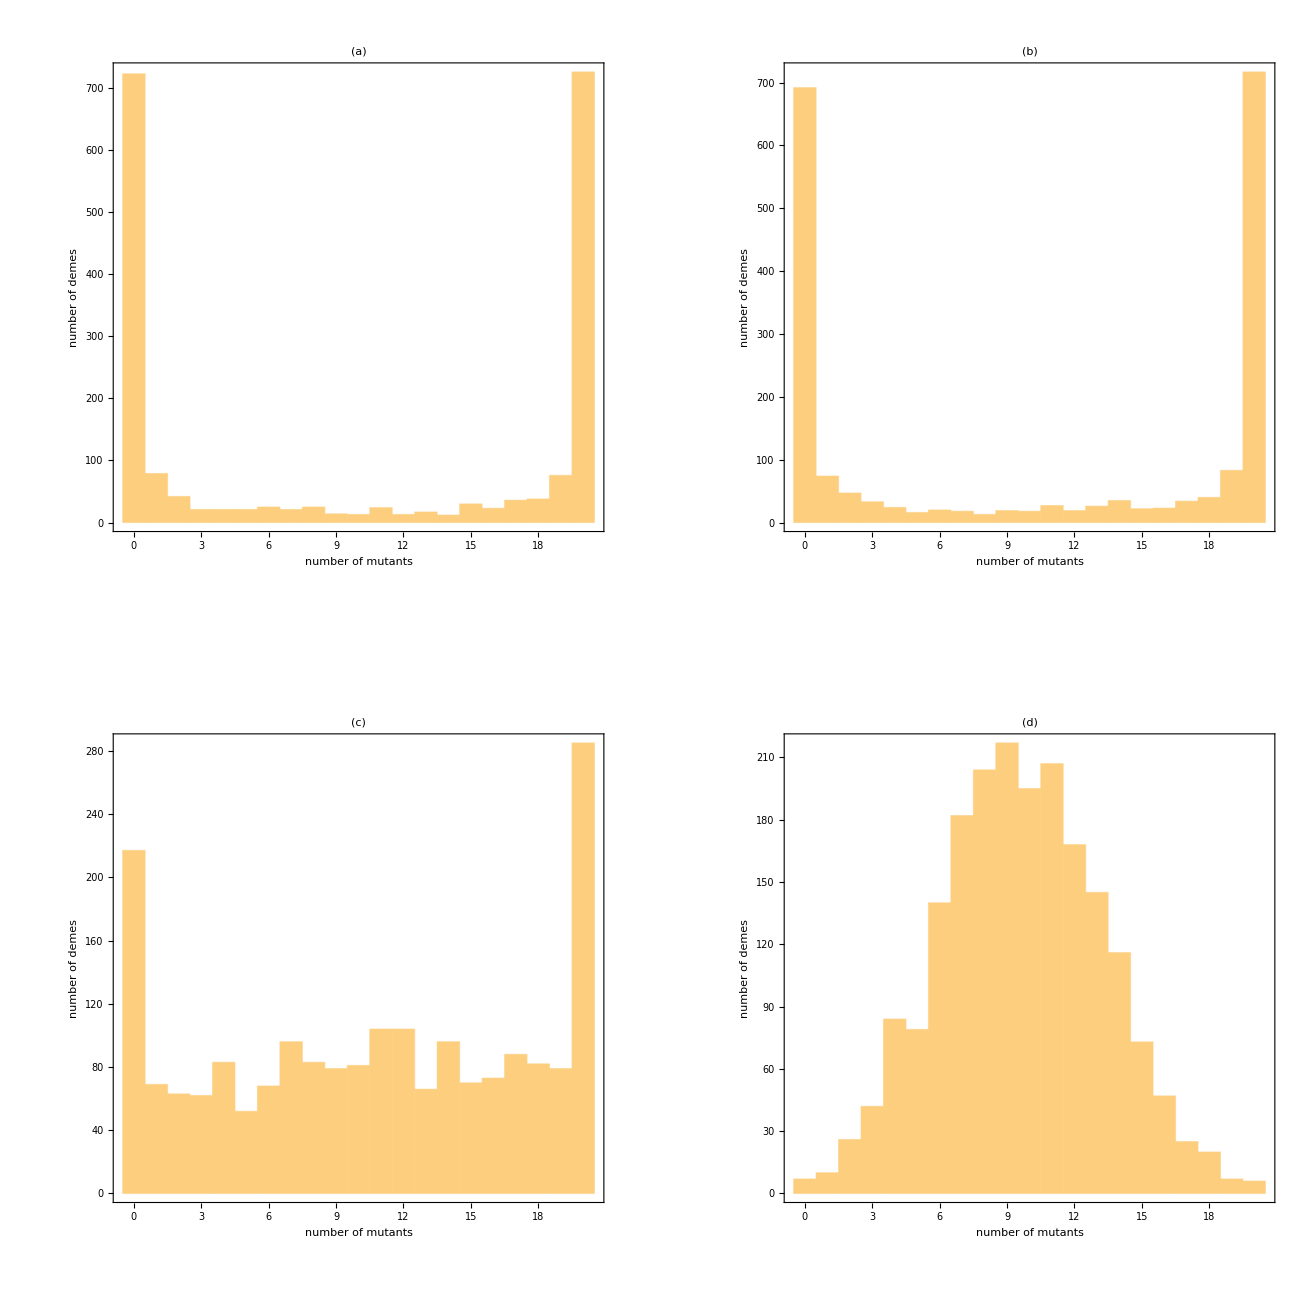

```mathematica
(* plot *)

no = Histogram[noXfin,Ncells,Frame->True,ImageSize->{600,600},FrameStyle->Bold,FrameLabel->{"number of mutants","number of demes"},PlotRange->{{-0.5,Ncells + 0.5},Full},PlotLabel->"(a)",AspectRatio-> Full,LabelStyle->{Bold,FontSize->36, FontColor->Black}];
medium = Histogram[mediumXfin,Ncells,Frame->True,ImageSize->{600,600},FrameStyle->Bold,FrameLabel->{"number of mutants","number of demes"},PlotRange->{{-0.5,Ncells + 0.5},Full},PlotLabel->"(b)",AspectRatio-> Full,LabelStyle->{Bold,FontSize->36, FontColor->Black}];
high = Histogram[highXfin,Ncells,Frame->True,ImageSize->{600,600},FrameStyle->Bold,FrameLabel->{"number of mutants","number of demes"},PlotRange->{{-0.5,Ncells + 0.5},Full},PlotLabel->"(c)",AspectRatio-> Full,LabelStyle->{Bold,FontSize->36, FontColor->Black}];
veryhigh = Histogram[veryhighXfin,Ncells,Frame->True,ImageSize->{600,600},FrameStyle->Bold,FrameLabel->{"number of mutants","number of demes"},PlotRange->{{-0.5,Ncells + 0.5},Full},PlotLabel->"(d)",AspectRatio-> Full,LabelStyle->{Bold,FontSize->36, FontColor->Black}];

GraphicsGrid[{{no,medium},{high,veryhigh}},ImageSize->{1300,1300},AspectRatio->Full]
```